```mathematica
canada= {{"Quebec", 1356128,1}, {"British Columbia", 925186,1},{"Ontario",917741,1},{"Alberta",642317,1},{"Saskatchewan",591670,1},{"Manitoba",553556,1},{"Newfoundland\nand Labrador",373872,1}}
chihuahua= {{"Chihuahua", 247455,2}}
usa = {{"Alaska",1477950,3},{"Texas",676588,3}, {"California", 403466,3}, {"Montana",376962,3}, {"New Mexico", 314160,3}, {"Arizona", 295233,3}, {"Nevada", 284331,3}, {"Colorado",268432,3}, {"Wyoming", 251470,3}, {"Oregon",248608,3},{"Idaho",214044,3}}
all = Join[canada,usa,chihuahua]
chartAll=Sort[all, #1[[2]]>#2[[2]]&]
colors = {RGBColor[.9,0,.1],RGBColor[0.99,0.75,0],RGBColor[.1,.1,.6]};
```

{{Quebec,1356128,1},{British Columbia,925186,1},{Ontario,917741,1},{Alberta,642317,1},{Saskatchewan,591670,1},{Manitoba,553556,1},{Newfoundland
and Labrador,373872,1}}

{{Chihuahua,247455,2}}

{{Alaska,1477950,3},{Texas,676588,3},{California,403466,3},{Montana,376962,3},{New Mexico,314160,3},{Arizona,295233,3},{Nevada,284331,3},{Colorado,268432,3},{Wyoming,251470,3},{Oregon,248608,3},{Idaho,214044,3}}

{{Quebec,1356128,1},{British Columbia,925186,1},{Ontario,917741,1},{Alberta,642317,1},{Saskatchewan,591670,1},{Manitoba,553556,1},{Newfoundland
and Labrador,373872,1},{Alaska,1477950,3},{Texas,676588,3},{California,403466,3},{Montana,376962,3},{New Mexico,314160,3},{Arizona,295233,3},{Nevada,284331,3},{Colorado,268432,3},{Wyoming,251470,3},{Oregon,248608,3},{Idaho,214044,3},{Chihuahua,247455,2}}

{{Alaska,1477950,3},{Quebec,1356128,1},{British Columbia,925186,1},{Ontario,917741,1},{Texas,676588,3},{Alberta,642317,1},{Saskatchewan,591670,1},{Manitoba,553556,1},{California,403466,3},{Montana,376962,3},{Newfoundland
and Labrador,373872,1},{New Mexico,314160,3},{Arizona,295233,3},{Nevada,284331,3},{Colorado,268432,3},{Wyoming,251470,3},{Oregon,248608,3},{Chihuahua,247455,2},{Idaho,214044,3}}

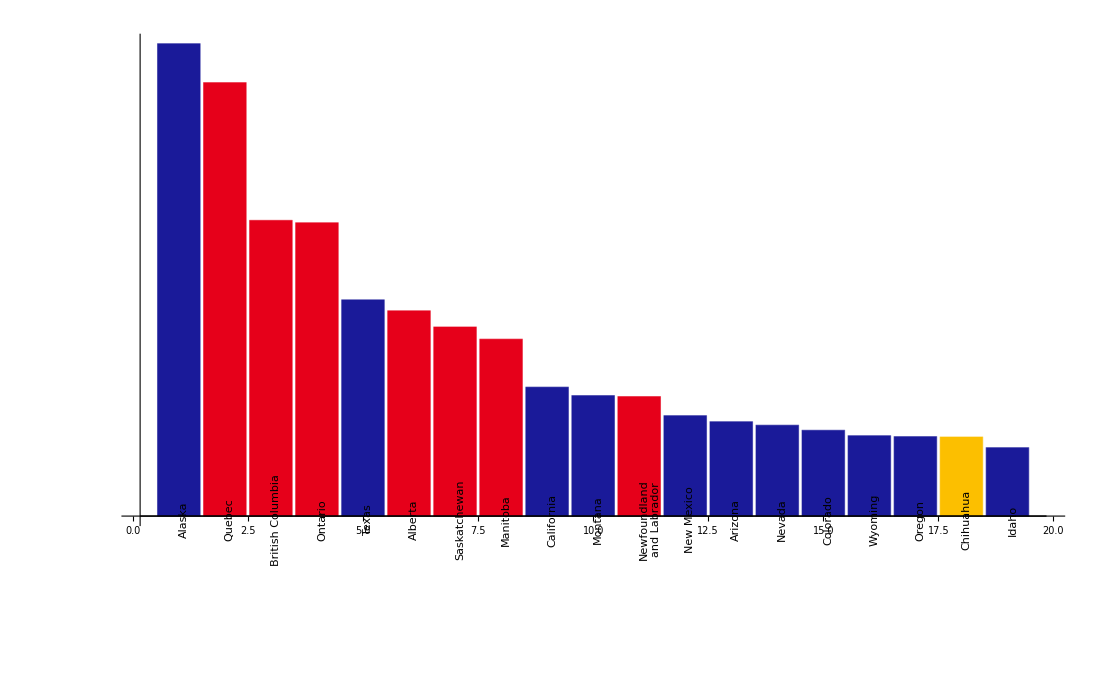

```mathematica
BarChart[chartAll[[All,2]],ChartStyle->colors[[chartAll[[All,3]]]],ChartLabels->Placed[chartAll[[All,1]],Below,Rotate[#,90Degree]&], Ticks->{Automatic, None}, AxesLabel->{None},  BaseStyle->{FontFamily->"Helvetica Neue",FontSize->16}]
```